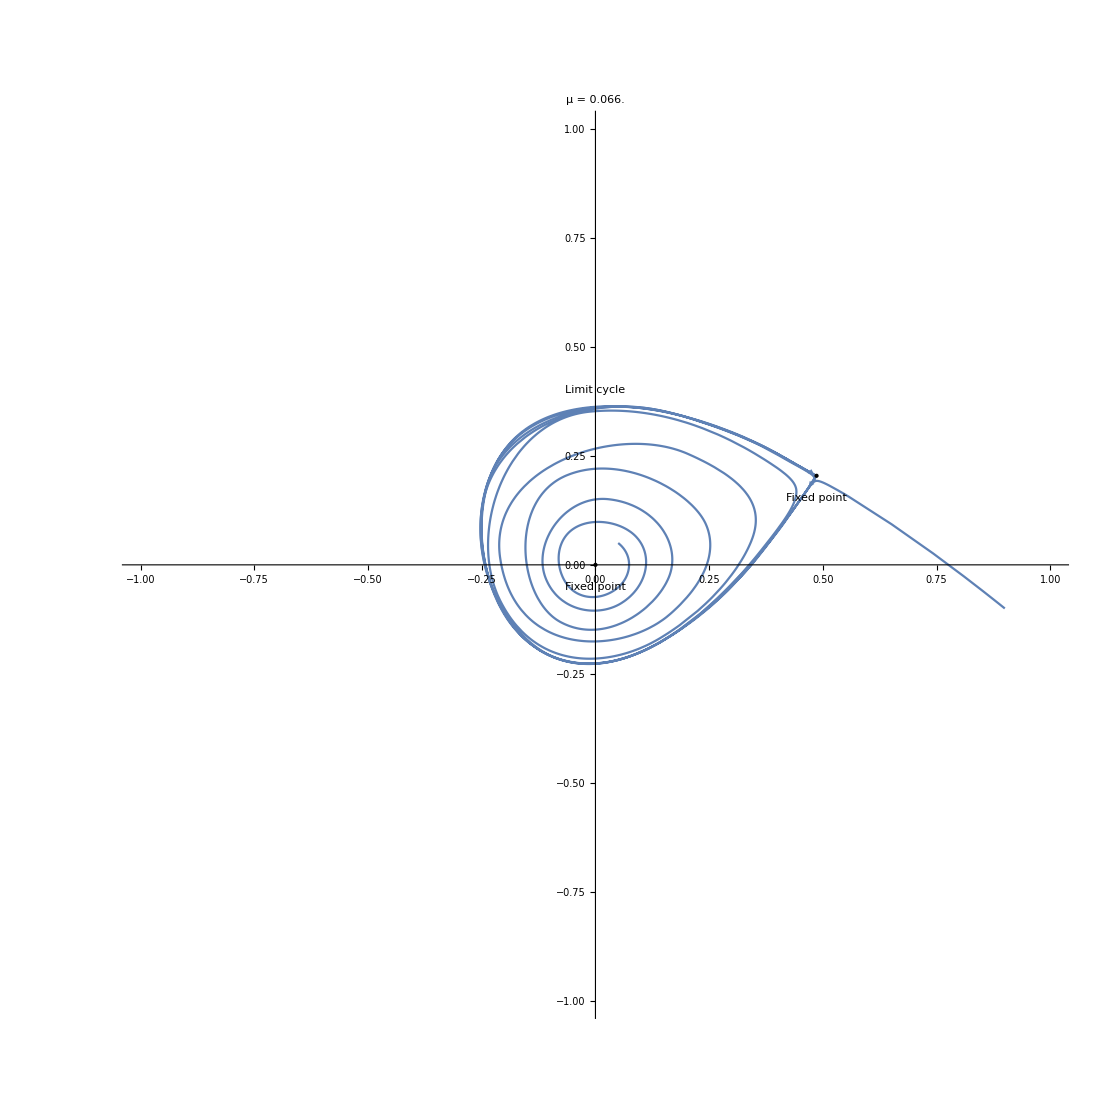

```mathematica
minxplot =-1;
maxxplot = 1;
minyplot = -1;
maxyplot = 1;

tMax = 50;
μ = 0.066;
title = StringForm["μ = `1`.", μ];

sol[u_, v_]:=NDSolve[{x'[t]== μ*x[t] + y[t] - x[t]^2,y'[t]==-x[t] + μ*y[t] + 2*x[t]^2,x[0]==u,y[0]==v},{x,y},{t,tMax}, Method->"StiffnessSwitching"]

p1 = ParametricPlot[Evaluate[{x[t],y[t]}/.sol[0.05, 0.05]], {t,0,tMax},PlotRange->{{minxplot,maxxplot},{minyplot,maxyplot}},PlotLabel->Style[title,FontSize->15]]/.Line[x_]:>{Arrowheads[{0.02,0.}],Arrow[x]};

p2 = ParametricPlot[Evaluate[{x[t],y[t]}/.sol[0.1, 0]], {t,0,tMax},PlotRange->{{minxplot,maxxplot},{minyplot,maxyplot}},PlotLabel->Style[title,FontSize->15]]/.Line[x_]:>{Arrowheads[{0.02,0.}],Arrow[x]};
p3 = ParametricPlot[Evaluate[{x[t],y[t]}/.sol[0.01, 0.01]], {t,0,tMax},PlotRange->{{minxplot,maxxplot},{minyplot,maxyplot}},PlotLabel->Style[title,FontSize->15]]/.Line[x_]:>{Arrowheads[{0.02,0.}],Arrow[x]};

miny = -0.9;
maxy = 0.9;
minx = -0.9;
maxx = 0.9;
step = 0.1;

Table11= Table[{minx, y}, {y, miny, maxy, step}];
Table12 = Table[{x,maxy}, {x, minx, maxx, step}];
Table13= Table[{maxx, y}, {y, miny, maxy,step}];
Table14= Table[{x, miny}, {x, minx, maxx, step}];

TableFinal = Join[Table11, Table12, Table13, Table14];
xStar = (μ^2+1)/(μ+2);
yStar = xStar^2 - μ*xStar;


Show[p1,
Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[TableFinal[[i,1]],TableFinal[[i,2]]]], {t,0,tMax},PlotRange->{{minxplot,maxxplot},{minyplot,maxyplot}},PlotLabel->Style[title,FontSize->15]]/.Line[x_]:>{Arrowheads[{0.02,0.}],Arrow[x]}, {i,Length[TableFinal]}],
Graphics[{PointSize[Large],Point[{0,0}]}],
Graphics[Text[Style["Fixed point",Large], {0,-0.05}]],
Graphics[{PointSize[Large],Point[{xStar,yStar}]}],
Graphics[Text[Style["Fixed point",Large], {xStar,yStar-0.05}]],
Graphics[Text[Style["Limit cycle", Large], {0,  0.4}]]
]
```

```mathematica
xStar = (μ^2+1)/(μ+2)
yStar = xStar^2 - μ*xStar
```

1/2

```mathematica
yStar
```

6